## Major Techniness {Name, Science, Technology, Engineering, Math}

```mathematica
techcoeff=
{{"African and African American Studies",0.1,0,0,0},{"American Studies",0.1,0,0,0},{"Anthropological Sciences",0.4,0.1,0,0},{"Anthropology",0.4,0,0,0},{"Archaeology",0.2,0.3,0.2,0},{"Art",0,0.1,0,0},{"Art History",0,0,0,0},{"Art Practice",0,0,0,0},{"Asian American Studies",0.1,0,0,0},{"Biological Sciences",1,0.3,0,0.2},{"Biology",1,0.3,0,0.2},{"Chemical Engineering",0.7,0.8,1,0.6},{"Chemistry",1,0.4,0.2,0.6},{"Chicana and Chicano Studies",0.1,0,0,0},{"Chicana/o Studies",0.1,0,0,0},{"Chinese",0,0,0,0},{"Civil Engineering",0.5,0.8,1,0.8},{"Classics",0,0,0,0},{"Communication",0.1,0.2,0,0},{"Comparative Literature",0,0,0,0},{"Comparative Studies in Race and Ethnicity",0.2,0,0,0},{"Computer Science",0.3,1,1,0.9},{"Cultural and Social Anthropology",0.3,0,0,0},{"Drama",0.1,0,0,0},{"Earth Systems",0.8,0.4,0.5,0.3},{"East Asian Studies",0.1,0,0,0},{"Economics",0.4,0.3,0.2,0.6},{"Electrical Engineering",0.7,1,1,1},{"Energy Resources Engineering",0.3,0.5,1,0.4},{"Engineering",0.5,0.8,1,0.7},{"English",0,0,0,0},{"English and French Literature",0,0,0,0},{"English and German Literatures",0,0,0,0},{"English and Italian Literature",0,0,0,0},{"English and Spanish Literature",0,0,0,0},{"Environmental Engineering",0.7,0.4,1,0.3},{"Environmental Systems Engineering",0.7,0.4,1,0.3},{"Feminist, Gender, and Sexuality Studies",0,0,0,0},{"Feminist Studies",0,0,0,0},{"Film and Media Studies",0,0,0,0},{"French",0,0,0,0},{"Geological and Environmental Sciences",0.7,0.4,0.2,0.3},{"Geophysics",0.9,0,0,0.3},{"German Studies",0,0,0,0},{"History",0.1,0,0,0},{"Human Biology",1,0.2,0,0.3},{"Humanities",0,0,0,0},{"Iberian & Latin American Cultures",0,0,0,0},{"Individually Designed Major",0,0,0,0},{"Industrial Engineering",0.2,0.3,1,0.4},{"International Policy Studies",0,0,0,0},{"International Relations",0.2,0,0,0},{"Italian",0,0,0,0},{"Japanese",0,0,0,0},{"Linguistics",0.4,0.6,0.2,0.6},{"Management Science and Engineering",0.3,0.6,0.4,0.7},{"Materials Science and Engineering",0.8,0.7,1,0.5},{"Mathematical and Computational Science",0,0.8,0.7,1},{"Mathematics",0,0.6,0.2,1},{"Mechanical Engineering",0.3,0.7,1,0.6},{"Music",0.3,0.2,0.1,0.1},{"Native American Studies",0,0,0,0},{"Petroleum Engineering",0.3,0.5,1,0.2},{"Philosophy",0,0,0,0.2},{"Philosophy and Religious Studies",0,0,0,0.1},{"Physics",1,0.3,0.2,0.9},{"Political Science",0,0,0,0},{"Psychology",0.8,0.2,0,0.1},{"Public Policy",0,0,0,0},{"Religious Studies",0,0,0,0},{"Science and Technology and Society",0.4,0.4,0.2,0},{"Science, Technology, and Society",0.4,0.4,0.2,0},{"Science Technology and Society",0.4,0.4,0.2,0},{"Slavic Languages and Literatures",0,0,0,0},{"Sociology",0.5,0.1,0,0.3},{"Spanish",0,0,0,0},{"Statistics",0,0.3,0.1,1},{"Symbolic Systems",0.3,0.7,0.6,0.6},{"Urban Studies",0.3,0,0,0.2}};
```

```mathematica
techtable=Dispatch[#[[1]]->#[[2;;]]&/@techcoeff];
techcolor=Dispatch[#[[1]]->(RGBColor[1-#,0,#]&@(Norm@#[[2;;]]/2))&/@techcoeff];
```

## Data

```mathematica
data15={{"Earth Systems",22,53,75,6,16,22,28,69,97},{"Energy Resources Engineering",8,5,13,51,19,70,59,24,83},{"Environmental Earth System Science",0,0,0,21,30,51,21,30,51},{"Environment and Resources",0,0,0,37,35,72,37,35,72},{"Geological and Environmental Sciences",2,6,8,32,32,64,34,38,72},{"Geophysics",6,1,7,51,31,82,57,32,89},{"Petroleum Engineering",0,0,0,33,5,38,33,5,38},{"African and African American Studies",5,13,18,0,0,0,5,13,18},{"African Studies",0,0,0,1,2,3,1,2,3},{"American Studies",11,19,30,0,0,0,11,19,30},{"Anthropological Sciences",0,0,0,0,2,2,0,2,2},{"Anthropology",3,24,27,29,49,78,32,73,105},{"Archaeology",1,6,7,0,0,0,1,6,7},{"Applied and Engineering Physics",0,0,0,2,0,2,2,0,2},{"Applied Physics",0,0,0,104,24,128,104,24,128},{"Art",0,0,0,1,2,3,1,2,3},{"Art History",3,17,20,13,14,27,16,31,47},{"Art Practice",3,11,14,3,7,10,6,18,24},{"Asian American Studies",1,0,1,0,0,0,1,0,1},{"Biology",92,109,201,90,84,174,182,193,375},{"Biophysics",0,0,0,29,16,45,29,16,45},{"Chemistry",22,21,43,165,68,233,187,89,276},{"Chicana/o Studies",1,0,1,0,0,0,1,0,1},{"Chinese",0,3,3,8,21,29,8,24,32},{"Classics",8,17,25,20,18,38,28,35,63},{"Communication",17,33,50,25,40,65,42,73,115},{"Comparative Literature",9,14,23,5,14,19,14,28,42},{"Comparative Studies in Race and Ethnicity",6,17,23,0,0,0,6,17,23},{"Cultural and Social Anthropology",0,0,0,0,3,3,0,3,3},{"Design",0,0,0,5,3,8,5,3,8},{"Documentary Film and Video",0,0,0,7,9,16,7,9,16},{"Drama",9,13,22,6,13,19,15,26,41},{"East Asian Studies",1,4,5,23,41,64,24,45,69},{"Economics",104,87,191,122,39,161,226,126,352},{"English",46,63,109,31,37,68,77,100,177},{"Feminist, Gender, and Sexuality Studies",2,2,40,0,0,0,2,2,4},{"Film and Media Studies",8,8,16,0,0,0,8,8,16},{"Financial Mathematics",0,0,0,2,0,2,2,0,2},{"French",2,16,18,1,9,10,3,25,28},{"French and Italian",0,0,0,1,0,1,1,0,1},{"Italian",0,4,4,2,3,5,2,7,9},{"German Studies",2,2,4,7,8,15,9,10,19},{"History",37,47,84,53,53,106,90,100,190},{"History and Humanities",0,0,0,0,2,2,0,2,2},{"Human Biology",93,230,323,0,0,0,93,230,323},{"Iberian & Latin American Cultures",1,9,10,3,15,18,4,24,28},{"International Policy Studies",0,0,0,18,26,44,18,26,44},{"International Relations",39,76,115,0,0,0,39,76,115},{"Japanese",2,2,4,7,7,14,9,9,18},{"Latin American Studies",0,0,0,3,8,11,3,8,11},{"Linguistics",6,8,14,18,19,37,24,27,51},{"Mathematical and Computational Science",54,29,83,0,0,0,54,29,83},{"Mathematics",67,13,80,69,11,80,136,24,160},{"Modern Thought and Literature",0,0,0,13,12,25,13,12,25},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",22,11,33,42,23,65,64,34,98},{"Native American Studies",1,2,3,0,0,0,1,2,3},{"Philosophy",25,7,32,41,8,49,66,15,81},{"Philosophy and Religious Studies",6,1,7,0,0,0,6,1,7},{"Physics",48,13,61,143,30,173,191,43,234},{"Political Science",46,43,89,44,50,94,90,93,183},{"Psychology",36,82,118,35,44,79,71,126,197},{"Public Policy",24,33,57,21,12,33,45,45,90},{"Religious Studies",1,2,3,15,13,28,16,15,31},{"Russian, East European and Eurasian Studies",0,0,0,1,1,2,1,1,2},{"Science, Technology, and Society",90,119,209,0,0,0,90,119,209},{"Slavic Languages and Literatures",5,4,9,5,6,11,10,10,20},{"Sociology",7,12,19,29,50,79,36,62,98},{"Spanish",0,5,5,4,2,6,4,7,11},{"Statistics",0,0,0,100,50,150,100,50,150},{"Symbolic Systems",67,49,116,6,2,8,73,51,124},{"Urban Studies",4,7,11,0,0,0,4,7,11},{"Aeronautics and Astronautics",0,0,0,168,34,202,168,34,202},{"Bioengineering",0,0,0,81,49,130,81,49,130},{"Chemical Engineering",52,22,74,107,37,144,159,59,218},{"Civil and Environmental Engineering",0,0,0,239,190,429,239,190,429},{"Civil Engineering",15,21,36,0,0,0,15,21,36},{"Computational and Mathematical Engineering",0,0,0,123,28,151,123,28,151},{"Computer Science",412,162,574,417,102,519,829,264,1093},{"Electrical Engineering",100,24,124,589,210,799,689,234,923},{"Engineering",145,131,276,16,8,24,161,139,300},{"Environmental Engineering",1,5,6,0,0,0,1,5,6},{"Environmental Systems Engineering",1,3,4,0,0,0,1,3,4},{"Individually Designed Major",3,5,8,0,0,0,3,5,8},{"Management Science and Engineering",95,47,142,246,84,330,341,131,472},{"Materials Science and Engineering",22,7,29,133,50,183,155,57,212},{"Mechanical Engineering",124,47,171,377,162,539,501,209,710}};data14= {{"Earth, Energy and Environmental Sciences",0,0,0,1,0,1,1,0,1},{"Earth Systems",37,59,96,5,18,23,42,77,119},{"Energy Resources Engineering",5,5,10,43,12,55,48,17,65},{"Environmental Earth System Science",0,0,0,26,27,53,26,27,53},{"Environment and Resources",0,0,0,40,39,79,40,39,79},{"Geological and Environmental Sciences",6,7,13,32,35,67,38,42,80},{"Geophysics",2,1,3,46,32,78,48,33,81},{"Petroleum Engineering",0,0,0,33,8,41,33,8,41},{"African and African American Studies",5,9,14,0,0,0,5,9,14},{"African Studies",0,0,0,1,2,3,1,2,3},{"American Studies",12,17,29,0,0,0,12,17,29},{"Anthropological Sciences",0,0,0,0,1,1,0,1,1},{"Anthropology",2,30,32,26,47,73,28,77,105},{"Archaeology",2,8,10,0,0,0,2,8,10},{"Applied Physics",0,0,0,99,27,126,99,27,126},{"Art",0,1,1,1,2,3,1,3,4},{"Art History",2,17,19,15,14,29,17,31,48},{"Art Practice",1,6,7,4,6,10,5,12,17},{"Asian American Studies",1,0,1,0,0,0,1,0,1},{"Biology",87,106,193,83,89,172,170,195,365},{"Biophysics",0,0,0,28,16,44,28,16,44},{"Chemistry",17,21,38,167,69,236,184,90,274},{"Chinese",0,1,1,5,21,26,5,22,27},{"Classics",15,12,27,20,15,35,35,27,62},{"Communication",17,36,53,24,34,58,41,70,111},{"Comparative Literature",5,8,13,5,14,19,10,22,32},{"Comparative Literature and Humanities",0,0,0,0,1,1,0,1,1},{"Comparative Studies in Race and Ethnicity",8,17,25,0,0,0,8,17,25},{"Cultural and Social Anthropology",0,0,0,1,5,6,1,5,6},{"Design",0,0,0,2,6,8,2,6,8},{"Documentary Film and Video",0,0,0,6,10,16,6,10,16},{"Drama",7,12,19,8,14,22,15,26,41},{"Drama and Humanities",0,0,0,2,0,2,2,0,2},{"East Asian Studies",2,2,4,25,35,60,27,37,64},{"Economics",110,59,169,125,45,170,235,104,339},{"English",34,64,98,31,35,66,65,99,164},{"Feminist Studies",0,1,1,0,0,0,0,1,1},{"Film and Media Studies",11,5,16,0,0,0,11,5,16},{"Financial Mathematics",0,0,0,19,3,22,19,3,22},{"French",3,19,22,3,11,14,6,30,36},{"French and Italian",0,0,0,1,0,1,1,0,1},{"Italian",0,6,6,1,3,4,1,9,10},{"German Studies",3,2,5,5,9,14,8,11,19},{"History",44,45,89,53,48,101,97,93,190},{"History and Humanities",0,0,0,0,2,2,0,2,2},{"Human Biology",73,240,313,0,0,0,73,240,313},{"Iberian & Latin American Cultures",1,5,6,4,11,15,5,16,21},{"Individually Designed Major",0,1,1,0,0,0,0,1,1},{"International Policy Studies",0,0,0,19,26,45,19,26,45},{"International Relations",45,74,119,0,0,0,45,74,119},{"Japanese",1,0,1,6,6,12,7,6,13},{"Latin American Studies",0,0,0,3,8,11,3,8,11},{"Linguistics",7,3,10,14,23,37,21,26,47},{"Mathematical and Computational Science",45,24,69,0,0,0,45,24,69},{"Mathematics",67,14,81,63,10,73,130,24,154},{"Modern Thought and Literature",0,0,0,13,12,25,13,12,25},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",23,13,36,35,26,61,58,39,97},{"Native American Studies",2,1,3,0,0,0,2,1,3},{"Philosophy",14,12,26,40,8,48,54,20,74},{"Philosophy and Religious Studies",4,0,4,0,0,0,4,0,4},{"Physics",43,13,56,137,35,172,180,48,228},{"Political Science",51,47,98,42,44,86,93,91,184},{"Psychology",39,77,116,37,47,84,76,124,200},{"Public Policy",27,28,55,19,8,27,46,36,82},{"Religious Studies",0,5,5,11,13,24,11,18,29},{"Russian and East European and Eurasian Studies",0,0,0,3,3,6,3,3,6},{"Science and Technology and Society",87,123,210,0,0,0,87,123,210},{"Slavic Languages and Literatures",4,4,8,7,5,12,11,9,20},{"Sociology",7,14,21,26,56,82,33,70,103},{"Spanish",1,4,5,6,4,10,7,8,15},{"Statistics",0,0,0,82,45,127,82,45,127},{"Symbolic Systems",54,44,98,6,1,7,60,45,105},{"Urban Studies",7,8,15,0,0,0,7,8,15},{"Aeronautics and Astronautics",0,0,0,171,28,199,171,28,199},{"Bioengineering",0,0,0,70,47,117,70,47,117},{"Chemical Engineering",46,22,68,98,42,140,144,64,208},{"Civil and Environmental Engineering",0,0,0,257,195,452,257,195,452},{"Civil Engineering",16,20,36,0,0,0,16,20,36},{"Computational and Mathematical Engineering",0,0,0,97,20,117,97,20,117},{"Computer Science",344,108,452,419,85,504,763,193,956},{"Electrical Engineering",83,18,101,626,204,830,709,222,931},{"Engineering",153,134,287,14,8,22,167,142,309},{"Environmental Engineering",2,6,8,0,0,0,2,6,8},{"Individually Designed Major",3,4,7,0,0,0,3,4,7},{"Industrial Engineering",0,1,1,0,0,0,0,1,1},{"Management Science and Engineering",104,38,142,252,98,350,356,136,492},{"Materials Science and Engineering",24,6,30,120,21,171,144,57,201},{"Mechanical Engineering",97,35,132,376,142,518,473,177,650},{"Scientific Computing and Computational Mathematics",0,0,0,1,0,1,1,0,1}};
data13={{"Earth Energy and Environmental Sciences",0,0,0,2,2,4,2,2,4},{"Earth Systems",42,54,96,7,19,26,49,73,122},{"Energy Resources Engineering",6,4,10,42,11,53,48,15,63},{"Environmental Earth System Science",0,0,0,23,24,47,23,24,47},{"Environment and Resources",0,0,0,49,31,80,49,31,80},{"Geological and Environmental Sciences",6,4,10,34,38,72,40,42,82},{"Geophysics",1,1,2,42,29,71,43,30,73},{"Petroleum Engineering",0,0,0,34,10,44,34,10,44},{"Aeronautics and Astronautics",0,0,0,165,24,189,165,24,189},{"Bioengineering",0,0,0,66,43,109,66,43,109},{"Chemical Engineering",42,18,60,90,45,135,132,63,195},{"Civil and Environmental Engineering",0,0,0,243,194,437,243,194,437},{"Civil Engineering",26,16,42,0,0,0,26,16,42},{"Computational and Mathematical Engineering",0,0,0,94,19,113,94,19,113},{"Computer Science",285,75,360,398,86,484,683,161,844},{"Electrical Engineering",77,18,95,704,192,896,781,210,991},{"Engineering",150,126,276,15,7,22,165,133,298},{"Environmental Engineering",7,11,18,0,0,0,7,11,18},{"Individually Designed Major",1,4,5,0,0,0,1,4,5},{"Industrial Engineering",0,1,1,0,0,0,0,1,1},{"Management Science and Engineering",89,38,127,269,98,367,358,136,494},{"Materials Science and Engineering",21,7,28,129,57,186,150,64,214},{"Mechanical Engineering",77,30,107,398,114,512,475,144,619},{"Scientific Computing and Computational Mathematics",0,0,0,1,0,1,1,0,1},{"African and African American Studies",2,6,8,0,0,0,2,6,8},{"African Studies",0,0,0,1,3,4,1,3,4},{"American Studies",9,22,31,0,0,0,9,22,31},{"Anthropological Sciences",0,0,0,1,1,2,1,1,2},{"Anthropology",5,36,41,22,44,66,27,80,107},{"Archaeology",3,6,9,0,0,0,3,6,9},{"Applied Physics",0,0,0,103,30,133,103,30,133},{"Art",0,0,0,1,5,6,1,5,6},{"Art History",3,14,17,12,15,27,15,29,44},{"Art Practice",4,9,13,7,3,10,11,12,23},{"Asian American Studies",1,3,4,0,0,0,1,3,4},{"Biology",78,115,193,80,84,164,158,199,357},{"Biophysics",0,0,0,19,13,32,19,13,32},{"Chemistry",30,24,54,147,71,218,177,95,272},{"Chicana and Chicano Studies",2,0,2,0,0,0,2,0,2},{"Chinese",0,0,0,4,14,18,4,14,18},{"Classics",21,10,31,19,14,33,40,24,64},{"Communication",18,32,50,21,35,56,39,67,106},{"Comparative Literature",3,11,14,3,16,19,6,27,33},{"Comparative Literature and Humanities",0,0,0,0,1,1,0,1,1},{"Comparative Studies in Race and Ethnicity",8,16,24,0,0,0,8,16,24},{"Cultural and Social Anthropology",0,0,0,3,8,11,3,8,11},{"Design",0,0,0,0,4,4,0,4,4},{"Documentary Film and Video",0,0,0,5,10,15,5,10,15},{"Drama",5,6,11,7,16,23,12,22,34},{"Drama and Humanities",0,0,0,2,1,3,2,1,3},{"East Asian Studies",1,4,5,24,43,67,25,47,72},{"Economics",113,65,178,116,44,160,229,109,338},{"English",44,72,116,28,42,70,72,114,186},{"Feminist Studies",1,2,3,0,0,0,1,2,3},{"Film and Media Studies",11,10,21,0,0,0,11,10,21},{"Financial Mathematics",0,0,0,32,6,38,32,6,38},{"French",3,19,22,6,7,13,9,26,35},{"French and Italian",0,0,0,1,0,1,1,0,1},{"Italian",1,9,10,0,5,5,1,14,15},{"German Studies",6,0,6,3,9,12,9,9,18},{"History",52,71,123,56,45,101,108,116,224},{"History and Humanities",0,0,0,0,2,2,0,2,2},{"Human Biology",68,261,329,0,0,0,68,261,329},{"Iberian & Latin American Cultures",3,3,6,3,7,10,6,10,16},{"Iberian & Latin American Cultures and Humanities",0,0,0,1,0,1,1,0,1},{"Individually Designed Major",1,1,2,0,0,0,1,1,2},{"International Policy Studies",0,0,0,18,24,42,18,24,42},{"International Relations",50,85,135,0,0,0,50,80,135},{"Japanese",3,2,5,5,9,14,8,11,19},{"Latin American Studies",0,0,0,2,6,8,2,6,9},{"Linguistics",8,7,15,17,21,38,25,28,53},{"Mathematical and Computational Science",32,21,53,0,0,0,32,21,53},{"Mathematics",60,15,75,65,10,75,125,25,150},{"Modern Thought and Literature",0,0,0,12,12,24,12,12,24},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",19,17,36,41,26,67,60,43,103},{"Native American Studies",2,0,2,0,0,0,2,0,2},{"Philosophy",15,11,26,37,13,50,52,24,76},{"Philosophy and Religious Studies",2,1,3,0,0,0,2,1,3},{"Physics",51,10,61,141,36,177,192,46,238},{"Political Science",55,50,105,42,48,90,97,98,195},{"Psychology",44,94,138,31,45,76,75,139,214},{"Public Policy",37,29,66,12,9,21,49,38,87},{"Religious Studies",2,5,7,11,7,18,13,12,25},{"Religious Studies and Humanities",0,0,0,1,0,1,1,0,1},{"Russian East European and Eurasian Studies",0,0,0,2,3,5,2,3,5},{"Science Technology and Society",88,98,186,0,0,0,88,98,186},{"Slavic Languages and Literatures",1,2,3,6,5,11,7,7,14},{"Sociology",12,19,31,28,53,81,40,72,112},{"Spanish",0,1,1,7,5,12,7,6,13},{"Statistics",0,0,0,85,46,131,85,46,131},{"Symbolic Systems",65,35,100,5,3,8,70,38,108},{"Urban Studies",10,22,32,0,0,0,10,22,32}};
data12={{"Earth, Energy and Environmental Sciences",0,0,0,2,2,4,2,2,4},{"Earth Systems",33,59,92,16,21,37,49,80,129},{"Energy Resources Engineering",5,1,6,41,11,52,46,12,58},{"Environmental Earth System Science",0,0,0,22,19,41,22,19,41},{"Environment and Resources",0,0,0,39,24,63,39,24,63},{"Geological and Environmental Sciences",4,5,9,35,38,73,39,43,82},{"Geophysics",1,1,2,41,27,68,42,28,70},{"Petroleum Engineering",0,0,0,25,9,34,25,9,34},{"African and African American Studies",3,6,9,0,0,0,3,6,9},{"African Studies",0,0,0,2,4,6,2,4,6},{"American Studies",10,22,32,0,0,0,10,22,32},{"Anthropological Sciences",0,0,0,1,3,4,1,3,4},{"Anthropology",3,33,36,15,38,53,18,71,89},{"Archaeology",2,6,8,0,0,0,2,6,8},{"Applied Physics",0,0,0,108,34,142,108,34,142},{"Art",0,0,0,3,6,9,3,6,9},{"Art History",3,11,14,10,13,23,13,24,37},{"Art Practice",4,18,22,6,4,10,10,22,32},{"Asian American Studies",1,3,4,0,0,0,1,3,4},{"Biology",86,110,196,84,77,161,170,187,357},{"Biophysics",0,0,0,18,13,31,18,13,31},{"Chemistry",39,19,58,139,77,216,178,96,274},{"Chicana and Chicano Studies",0,1,1,0,0,0,0,1,1},{"Chinese",2,2,4,5,10,15,7,12,19},{"Classics",21,18,39,17,17,34,38,35,73},{"Classics and Humanities",0,0,0,1,0,1,1,0,1},{"Communication",16,34,50,27,33,60,43,67,110},{"Comparative Literature",6,8,14,5,15,20,11,23,34},{"Comparative Studies in Race and Ethnicity",10,29,39,0,0,0,10,29,39},{"Cultural and Social Anthropology",0,0,0,6,8,14,6,8,14},{"Design",0,0,0,3,1,4,3,1,4},{"Documentary Film and Video",0,0,0,6,10,16,6,10,16},{"Drama",8,11,19,6,13,19,14,24,38},{"Drama and Humanities",0,0,0,2,2,4,2,2,4},{"East Asian Studies",2,7,9,21,23,44,23,30,53},{"Economics",115,58,173,98,41,139,213,99,312},{"English",40,84,124,32,35,67,72,119,191},{"English and French Literature",0,2,2,0,0,0,0,2,2},{"Feminist Studies",2,2,4,0,0,0,2,2,4},{"Film and Media Studies",9,15,24,0,0,0,9,15,24},{"Financial Mathematics",0,0,0,23,10,33,23,10,33},{"French",1,15,16,5,9,14,6,24,30},{"French and Italian",0,0,0,1,0,1,1,0,1},{"Italian",2,4,6,0,8,8,2,12,14},{"German Studies",5,1,6,4,11,15,9,12,21},{"History",55,73,128,57,42,99,112,115,227},{"History and Humanities",0,0,0,3,1,4,3,1,4},{"Human Biology",74,269,343,0,0,0,74,269,343},{"Iberian & Latin American Cultures",3,7,10,11,14,25,14,21,35},{"Iberian & Latin American Cultures and Humanities",0,0,0,1,0,1,1,0,1},{"Individually Designed Major",2,0,2,0,0,0,2,0,2},{"International Policy Studies",0,0,0,16,31,47,16,31,47},{"International Relations",57,98,155,0,0,0,57,98,155},{"Japanese",7,1,8,7,8,15,14,9,23},{"Latin American Studies",0,0,0,5,7,12,5,7,12},{"Linguistics",5,13,18,18,19,37,23,32,55},{"Mathematical and Computational Science",38,18,56,0,0,0,38,18,56},{"Mathematics",79,19,98,62,13,75,141,32,173},{"Modern Thought and Literature",0,0,0,13,13,26,13,13,26},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",25,14,39,40,26,66,65,40,105},{"Native American Studies",2,1,3,0,0,0,2,1,3},{"Philosophy",15,14,29,40,16,56,55,30,85},{"Philosophy and Religious Studies",1,0,1,0,0,0,1,0,1},{"Physics",41,12,53,137,31,168,178,43,221},{"Political Science",60,49,109,38,36,74,98,85,183},{"Psychology",44,124,168,31,49,80,75,173,248},{"Public Policy",30,31,61,13,7,20,43,38,81},{"Religious Studies",0,6,6,14,14,28,14,20,34},{"Russian, East European and Eurasian Studies",0,0,0,1,3,4,1,3,4},{"Science, Technology, and Society",74,56,130,0,0,0,74,56,130},{"Slavic Languages and Literatures",0,2,2,5,3,8,5,5,10},{"Sociology",19,24,43,21,56,77,40,80,120},{"Statistics",0,0,0,78,30,108,78,30,108},{"Symbolic Systems",60,22,82,11,3,14,71,25,96},{"Urban Studies",11,26,37,0,0,0,11,26,37},{"Aeronautics and Astronautics",0,0,0,159,31,190,159,31,190},{"Bioengineering",0,0,0,62,40,102,62,40,102},{"Chemical Engineering",36,23,59,76,44,120,112,67,179},{"Civil and Environmental Engineering",0,0,0,257,161,418,257,161,418},{"Civil Engineering",25,13,38,0,0,0,25,13,38},{"Computational and Mathematical Engineering",0,0,0,95,18,113,95,18,113},{"Computer Science",227,60,287,403,68,471,630,128,758},{"Electrical Engineering",69,19,88,709,188,897,778,207,985},{"Engineering",134,93,227,16,4,20,150,97,247},{"Environmental Engineering",8,12,20,0,0,0,8,12,20},{"Individually Designed Major",2,3,5,0,0,0,2,3,5},{"Industrial Engineering",0,1,1,0,0,0,0,1,1},{"Management Science and Engineering",104,42,146,299,132,431,403,174,577},{"Materials Science and Engineering",30,12,42,124,51,175,154,63,217},{"Mechanical Engineering",72,28,100,421,118,539,493,146,639},{"Scientific Computing and Computational Mathematics",0,0,0,2,0,2,2,0,2}};
data11={{"Earth, Energy and Environmental Sciences",0,0,0,2,3,5,2,3,5},{"Earth Systems",48,70,118,15,17,32,63,87,150},{"Energy Resources Engineering",7,2,9,39,13,52,46,15,61},{"Environmental Earth System Science",0,0,0,13,14,27,13,14,27},{"Environment and Resources",0,0,0,46,31,77,46,31,77},{"Geological and Environmental Sciences",6,5,11,30,31,61,36,36,72},{"Geophysics",0,0,0,43,20,63,43,20,63},{"Petroleum Engineering",0,0,0,29,7,36,29,7,36},{"Aeronautics and Astronautics",0,0,0,157,37,194,157,37,194},{"Bioengineering",0,0,0,65,39,104,65,39,104},{"Chemical Engineering",26,23,49,75,50,125,101,73,174},{"Civil and Environmental Engineering",0,0,0,260,161,421,260,161,421},{"Civil Engineering",19,13,32,0,0,0,19,13,32},{"Computational and Mathematical Engineering",0,0,0,101,17,118,101,17,118},{"Computer Science",200,47,247,398,68,466,598,115,713},{"Electrical Engineering",72,20,92,719,188,907,791,208,999},{"Engineering",125,83,208,15,4,19,140,87,227},{"Environmental Engineering",3,10,13,0,0,0,3,10,13},{"Individually Designed Major",1,2,3,0,0,0,1,2,3},{"Management Science and Engineering",96,44,140,300,120,420,396,164,560},{"Materials Science and Engineering",24,16,40,124,45,169,148,61,209},{"Mechanical Engineering",79,25,104,427,112,539,506,137,643},{"Scientific Computing and Computational Mathematics",0,0,0,2,0,2,2,0,2},{"African and African American Studies",1,3,4,0,0,0,1,3,4},{"African Studies",0,0,0,1,4,5,1,4,5},{"American Studies",12,17,29,0,0,0,12,17,29},{"Anthropological Sciences",1,2,3,4,6,10,5,8,13},{"Anthropology",7,35,42,18,29,47,25,64,89},{"Archaeology",4,6,10,0,0,0,4,6,10},{"Applied Physics",0,0,0,105,34,139,105,34,139},{"Art",1,1,2,10,17,27,11,18,29},{"Art History",7,16,23,9,12,21,16,28,44},{"Art Practice",8,26,34,2,3,5,10,29,39},{"Asian American Studies",1,3,4,0,0,0,1,3,4},{"Biology",97,120,217,82,83,165,179,203,382},{"Biophysics",0,0,0,15,14,29,15,14,29},{"Chemistry",32,18,50,140,82,222,172,100,272},{"Chicana and Chicano Studies",0,1,1,0,0,0,0,1,1},{"Chinese",2,1,3,1,12,13,3,13,16},{"Classics",23,17,40,15,17,32,38,34,72},{"Classics and Humanities",0,0,0,1,0,1,1,0,1},{"Communication",18,58,76,27,33,60,45,91,136},{"Comparative Literature",6,11,17,8,13,21,14,24,38},{"Comparative Studies in Race and Ethnicity",4,26,30,0,0,0,4,26,30},{"Cultural and Social Anthropology",0,1,1,8,14,22,8,15,23},{"Design",0,0,0,3,3,6,3,3,6},{"Documentary Film and Video",0,0,0,6,10,16,6,10,16},{"Drama",9,9,18,7,11,18,16,20,36},{"Drama and Humanities",0,0,0,3,2,5,3,2,5},{"East Asian Studies",5,5,10,19,27,46,24,32,56},{"Economics",135,59,194,95,42,137,230,101,331},{"English",43,92,135,33,35,68,76,127,203},{"English and French Literature",0,4,4,0,0,0,0,4,4},{"English and Italian Literature",0,1,1,0,0,0,0,1,1},{"Feminist Studies",2,1,3,0,0,0,2,1,3},{"Film and Media Studies",9,12,21,0,0,0,9,12,21},{"Financial Mathematics",0,0,0,24,8,32,24,8,32},{"French",0,6,6,4,9,13,4,15,19},{"French and Italian",0,0,0,1,2,3,1,2,3},{"Italian",2,4,6,2,6,8,4,10,14},{"German Studies",4,0,4,4,8,12,8,8,16},{"German Studies and Humanities",0,0,0,1,0,1,1,0,1},{"History",50,61,111,52,46,98,102,107,209},{"History and Humanities",0,0,0,4,2,6,4,2,6},{"Human Biology",83,246,329,0,0,0,83,246,329},{"Iberian & Latin American Cultures",4,11,15,10,10,20,14,21,35},{"Iberian & Latin American Cultures and Humanities",0,0,0,1,1,2,1,1,2},{"Individually Designed Major",1,4,5,0,0,0,1,4,5},{"International Policy Studies",0,1,1,11,30,41,11,31,42},{"International Relations",70,115,185,0,0,0,70,115,185},{"Japanese",3,3,6,10,7,17,13,10,23},{"Latin American Studies",0,0,0,3,6,9,3,6,9},{"Linguistics",3,13,16,16,15,31,19,28,47},{"Mathematical and Computational Science",33,16,49,0,0,0,33,16,49},{"Mathematics",81,18,99,61,12,73,142,30,172},{"Modern Thought and Literature",0,0,0,11,14,25,11,14,25},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",29,14,43,35,22,57,64,36,100},{"Music and Humanities",0,0,0,1,0,1,1,0,1},{"Native American Studies",1,1,2,0,0,0,1,1,2},{"Philosophy",20,16,36,43,13,56,63,29,92},{"Philosophy and Religious Studies",6,2,8,0,0,0,6,2,8},{"Physics",48,14,62,135,33,168,183,47,230},{"Political Science",69,55,124,39,42,81,108,97,205},{"Psychology",39,117,156,34,49,83,73,166,239},{"Public Policy",24,33,57,11,6,17,35,39,74},{"Religious Studies",2,2,4,13,13,26,15,15,30},{"Religious Studies and Humanities",0,0,0,1,0,1,1,0,0},{"Russian, East European and Eurasian Studies",0,0,0,4,5,9,4,5,9},{"Science, Technology, and Society",64,44,108,0,0,0,64,44,108},{"Slavic Languages and Literatures",0,2,2,6,5,11,6,7,13},{"Sociology",14,18,32,25,60,85,39,78,117},{"Statistics",1,0,1,76,28,104,77,28,105},{"Symbolic Systems",34,19,53,12,2,14,46,21,67},{"Urban Studies",15,24,39,0,0,0,15,24,39}};
data10={{"Earth, Energy and Environmental Sciences",0,0,0,4,4,8,4,4,8},{"Earth Systems",44,68,112,13,11,24,57,79,136},{"Energy Resources Engineering",11,0,11,30,10,40,41,10,51},{"Environmental Earth System Science",0,0,0,12,10,22,12,10,22},{"Geological and Environmental Sciences",7,8,15,29,33,62,36,41,77},{"Geophysics",1,1,2,36,18,54,37,19,56},{"Interdisciplinary Program in Environment and Resources",0,0,0,31,31,62,31,31,62},{"Petroleum Engineering",0,0,0,35,11,46,35,11,46},{"Aeronautics and Astronautics",0,0,0,152,32,184,152,32,184},{"Bioengineering",0,0,0,59,39,98,59,39,98},{"Chemical Engineering",34,20,54,64,44,108,98,64,162},{"Civil and Environmental Engineering",0,0,0,225,139,364,225,139,364},{"Civil Engineering",16,17,33,0,0,0,16,17,33},{"Computational and Mathematical Engineering",0,0,0,96,25,121,96,25,121},{"Computer Science",164,25,189,401,61,462,565,86,651},{"Electrical Engineering",66,12,78,718,188,906,784,200,984},{"Engineering",108,80,188,16,5,21,124,85,209},{"Environmental Engineering",7,8,15,0,0,0,7,8,15},{"Individually Designed Major",0,2,2,0,0,0,0,2,2},{"Management Science and Engineering",97,32,129,265,103,368,362,135,497},{"Materials Science and Engineering",12,12,24,133,40,173,145,52,197},{"Mechanical Engineering",72,19,91,389,117,506,461,136,597},{"Scientific Computing and Computational Mathematics",0,0,0,2,0,2,2,0,2},{"African and African American Studies",2,3,5,0,0,0,2,3,5},{"African Studies",0,0,0,0,2,2,0,2,2},{"American Studies",7,20,27,0,0,0,7,20,27},{"Anthropological Sciences",0,3,3,9,5,14,9,8,17},{"Anthropology",5,25,30,14,18,32,19,43,62},{"Archaeology",5,5,10,0,0,0,5,5,10},{"Applied Physics",0,0,0,103,36,139,103,36,139},{"Art",7,28,35,16,26,42,23,54,77},{"Art and Humanities",0,0,0,0,1,1,0,1,1},{"Art History",1,4,5,0,2,2,1,6,7},{"Art Practice",1,5,6,0,0,0,1,5,6},{"Asian American Studies",1,2,3,0,0,0,1,2,3},{"Chinese",5,5,10,3,9,12,8,14,22},{"Japanese",2,4,6,5,7,12,7,11,18},{"Biology",96,131,227,83,74,157,179,205,384},{"Biophysics",0,0,0,21,10,31,21,10,31},{"Chemistry",25,21,46,139,74,213,164,95,259},{"Chicana and Chicano Studies",0,1,1,0,0,0,0,1,1},{"Classics",20,23,43,12,11,23,32,34,65},{"Communication",23,51,74,23,29,52,46,80,126},{"Comparative Literature",12,11,23,9,12,21,21,23,44},{"Comparative Studies in Race and Ethnicity",3,15,18,0,0,0,3,15,18},{"Cultural and Social Anthropology",1,1,2,10,20,30,11,21,32},{"Design",0,0,0,0,1,1,0,1,1},{"Documentary Film and Video",0,0,0,9,7,16,9,7,16},{"Drama",4,12,16,7,12,19,11,24,35},{"Drama and Humanities",0,0,0,4,0,4,4,0,4},{"East Asian Studies",4,5,9,20,25,45,24,30,54},{"Economics",143,86,229,97,42,139,240,128,368},{"English",41,80,121,32,36,68,73,116,189},{"English and French Literature",0,2,2,0,0,0,0,2,2},{"Feminist Studies",0,5,5,0,0,0,0,5,5},{"Film and Media Studies",8,7,15,0,0,0,8,7,15},{"Financial Mathematics",0,0,0,42,8,50,42,8,50},{"French",0,8,8,2,10,12,2,18,20},{"French and Italian",0,0,0,0,2,2,0,2,2},{"Italian",2,4,6,2,5,7,4,9,13},{"French and Humanities",0,0,0,0,1,1,0,1,1},{"German Studies",2,1,3,4,5,9,6,6,12},{"History",54,63,117,48,49,97,102,112,214},{"History and Humanities",0,0,0,3,2,5,3,2,5},{"Human Biology",83,283,366,0,0,0,83,283,366},{"Humanities",0,6,6,0,0,0,0,6,6},{"Iberian & Latin American Cultures",5,12,17,12,9,21,17,21,38},{"Iberian & Latin American Cultures and Humanities",0,0,0,0,1,1,0,1,1},{"Individually Designed Major",1,1,2,0,0,0,1,1,2},{"International Policy Studies",0,1,1,12,27,39,12,28,40},{"International Relations",76,105,181,0,0,0,76,105,181},{"Latin American Studies",0,0,0,5,6,11,5,6,11},{"Linguistics",3,9,12,13,17,30,16,26,42},{"Mathematical and Computational Science",36,14,50,0,0,0,36,14,50},{"Mathematics",61,21,82,57,15,72,118,36,154},{"Modern Thought and Literature",0,0,0,9,12,21,9,12,21},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",31,16,47,39,20,59,70,36,106},{"Music and Humanities",0,0,0,1,1,2,1,1,2},{"Native American Studies",1,1,2,0,0,0,1,1,2},{"Philosophy",15,10,25,41,14,55,56,24,80},{"Philosophy and Religious Studies",5,3,8,0,0,0,5,3,8},{"Physics",54,18,72,131,35,166,185,53,238},{"Political Science",66,64,130,43,37,80,109,101,210},{"Psychology",41,108,149,27,47,74,68,155,223},{"Public Policy",27,27,54,10,7,17,37,34,71},{"Religious Studies",2,2,4,16,10,26,18,12,30},{"Russian, East European and Eurasian Studies",0,0,0,8,2,10,8,2,10},{"Science, Technology, and Society",58,41,99,0,0,0,58,41,99},{"Slavic Languages and Literatures",2,3,5,7,4,11,9,7,16},{"Sociology",16,27,43,30,56,86,46,83,129},{"Statistics",1,0,1,87,27,114,88,27,115},{"Symbolic Systems",38,16,54,3,0,3,41,16,57},{"Urban Studies",12,18,30,0,0,0,12,18,30}};
data09={{"Earth, Energy and Environmental Sciences",0,0,0,7,5,12,7,5,12},{"Earth Systems",30,45,75,3,7,10,33,52,85},{"Energy Resources Engineering",5,2,7,10,6,16,15,8,23},{"Environmental Earth System Science",0,0,0,10,10,20,10,10,20},{"Geological and Environmental Sciences",11,8,19,39,40,79,50,48,98},{"Geophysics",1,1,2,30,19,49,31,20,51},{"Interdisciplinary Program in Environment and Resources",0,0,0,22,20,42,22,20,42},{"Petroleum Engineering",0,0,0,45,14,59,45,14,59},{"Aeronautics and Astronautics",0,0,0,164,28,192,164,28,192},{"Bioengineering",0,0,0,50,37,87,50,37,87},{"Chemical Engineering",25,17,42,73,40,113,98,57,155},{"Civil and Environmental Engineering",0,0,0,193,139,332,193,139,322},{"Civil Engineering",14,18,32,0,0,0,14,18,32},{"Computational and Mathematical Engineering",0,0,0,87,20,107,87,20,107},{"Computer Science",122,19,141,367,51,418,490,70,560},{"Electrical Engineering",64,13,77,764,180,944,828,193,1021},{"Engineering",109,72,181,13,6,19,122,78,200},{"Environmental Engineering",3,10,13,0,0,0,3,10,13},{"Individually Designed Major",1,4,5,0,0,0,1,4,5},{"Management Science and Engineering",69,34,103,261,108,369,330,142,472},{"Materials Science and Engineering",12,7,19,138,35,173,150,42,192},{"Mechanical Engineering",68,14,82,415,121,536,483,135,618},{"Scientific Computing and Computational Mathematics",0,0,0,8,0,8,8,0,8},{"African and African American Studies",1,0,1,0,0,0,1,0,1},{"African Studies",0,0,0,1,1,2,1,1,2},{"American Studies",8,32,40,0,0,0,8,32,40},{"Anthropological Sciences",1,12,13,10,8,18,11,20,31},{"Anthropology",2,12,14,6,10,16,8,22,30},{"Archaeology",1,5,6,0,0,0,1,5,6},{"Applied Physics",0,0,0,111,36,147,111,36,147},{"Art",7,28,35,24,26,50,31,54,85},{"Art and Humanities",0,0,0,0,1,1,0,1,1},{"Asian American Studies",1,3,4,0,0,0,1,3,4},{"Chinese",7,5,12,4,10,14,11,15,26},{"Japanese",2,5,7,8,6,14,10,11,21},{"Biology",102,116,218,88,87,175,190,203,393},{"Biophysics",0,0,0,23,9,32,23,9,32},{"Chemistry",27,20,47,132,68,200,159,88,247},{"Chicana and Chicano Studies",0,2,2,0,0,0,0,2,2},{"Classics",18,22,40,11,14,25,29,36,65},{"Communication",32,43,75,22,35,57,54,78,132},{"Comparative Literature",8,13,21,10,10,20,18,23,41},{"Comparative Studies in Race and Ethnicity",7,12,19,0,0,0,7,12,19},{"Cultural and Social Anthropology",4,11,15,9,25,34,13,36,49},{"Documentary Film and Video",0,0,0,9,7,16,9,7,16},{"Drama",5,15,20,8,10,18,13,25,38},{"Drama and Humanities",0,0,0,1,1,2,1,1,2},{"East Asian Studies",3,3,6,15,14,29,18,17,35},{"Economics",136,89,225,95,38,133,231,127,358},{"English",44,79,123,25,41,66,69,120,189},{"English and German Literatures",1,0,1,0,0,0,1,0,1},{"English and Spanish Literature",0,1,1,0,0,0,0,1,1},{"Feminist Studies",1,4,5,0,0,0,1,4,5},{"Film and Media Studies",7,8,15,0,0,0,7,8,15},{"Financial Mathematics",0,0,0,61,15,76,61,15,76},{"French",1,3,4,2,9,11,3,12,15},{"French and Italian",0,0,0,0,2,2,0,2,2},{"Italian",1,1,2,2,4,6,3,5,8},{"French and Humanities",0,0,0,0,1,1,0,1,1},{"German Studies",3,6,9,4,5,9,7,11,18},{"German Studies and Humanities",0,0,0,1,0,1,1,0,1},{"History",65,51,116,43,52,95,108,103,211},{"History and Humanities",0,0,0,3,0,3,3,0,3},{"Human Biology",113,277,390,0,0,0,113,277,390},{"Humanities",3,9,12,1,1,2,4,10,14},{"Individually Designed Major",1,1,2,0,0,0,1,1,2},{"International Policy Studies",0,0,0,16,22,38,16,22,38},{"International Relations",70,99,169,0,0,0,70,99,169},{"Latin American Studies",0,0,0,3,6,9,3,6,9},{"Linguistics",2,6,8,13,23,36,15,29,44},{"Mathematical and Computational Science",33,16,49,0,0,0,33,16,49},{"Mathematics",70,19,89,59,14,73,129,33,162},{"Modern Thought and Literature",0,0,0,13,13,26,13,13,26},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",22,16,38,30,22,52,52,38,90},{"Music and Humanities",0,0,0,2,2,4,2,2,4},{"Native American Studies",1,5,6,0,0,0,1,5,6},{"Philosophy",22,11,33,37,17,54,59,28,87},{"Philosophy and Religious Studies",2,2,4,0,0,0,2,2,4},{"Physics",49,14,63,146,32,178,195,46,241},{"Political Science",51,66,117,41,31,72,92,97,189},{"Psychology",32,98,130,38,49,87,70,147,217},{"Public Policy",28,23,51,5,3,8,33,26,59},{"Religious Studies",3,5,8,17,7,24,20,12,32},{"Russian, East European and Eurasian Studies",0,0,0,5,4,9,5,4,9},{"Science, Technology, and Society",36,29,65,0,0,0,36,29,65},{"Slavic Languages and Literatures",3,7,10,5,3,8,8,10,18},{"Sociology",27,41,68,32,60,92,59,101,160},{"Spanish",5,12,17,7,11,18,12,23,35},{"Spanish and Humanities",0,0,0,1,1,2,1,1,2},{"Statistics",0,0,0,75,23,98,75,23,98},{"Symbolic Systems",44,20,64,5,0,5,49,20,69},{"Urban Studies",7,15,22,0,0,0,7,15,22}};
data08={{"Earth, Energy, and Environmental Sciences",0,0,0,4,8,12,4,8,12},{"Earth Systems",24,35,59,1,7,8,25,42,67},{"Energy Resources Engineering",0,0,0,2,0,2,2,0,2},{"Geological and Environmental Sciences",10,9,19,36,43,79,46,52,98},{"Geophysics",0,0,0,36,15,51,36,15,51},{"Interdisciplinary Program in Environment and Resources",0,0,0,14,19,33,14,19,33},{"Petroleum Engineering",1,0,1,46,16,62,47,16,63},{"Aeronautics and Astronautics",0,0,0,180,34,214,180,34,214},{"Bioengineering",0,0,0,43,31,74,43,31,74},{"Chemical Engineering",28,15,43,59,34,93,87,49,136},{"Civil and Environmental Engineering",0,0,0,160,111,271,160,111,271},{"Civil Engineering",17,13,30,0,0,0,17,13,30},{"Computational and Mathematical Engineering",0,0,0,80,16,96,80,16,96},{"Computer Science",126,16,142,329,46,375,455,62,517},{"Electrical Engineering",75,17,92,781,177,958,856,194,1050},{"Engineering",93,68,161,6,3,9,99,71,170},{"Engineering-Economic Systems and Operations Research",0,0,0,0,1,1,0,1,1},{"Environmental Engineering",3,5,8,0,0,0,3,5,8},{"Individually Designed Major",0,2,2,0,0,0,0,2,2},{"Management Science and Engineering",82,32,114,285,113,398,367,145,512},{"Materials Science and Engineering",16,3,19,103,33,136,119,36,155},{"Mechanical Engineering",66,21,87,411,115,526,477,136,613},{"Scientific Computing and Computational",0,0,0,12,4,16,12,4,16},{"African and African American Studies",0,2,2,0,0,0,0,2,2},{"African Studies",0,0,0,0,1,1,0,1,1},{"American Studies",8,30,38,0,0,0,8,30,38},{"Anthropological Sciences",5,21,26,15,15,30,20,36,56},{"Anthropology",0,0,0,0,3,3,0,3,3},{"Archaeology",1,4,5,0,0,0,1,4,5},{"Applied Physics",0,0,0,118,36,154,118,36,154},{"Art",7,41,48,18,26,44,25,67,92},{"Asian American Studies",0,1,1,0,0,0,0,1,1},{"Chinese",2,4,6,2,11,13,4,15,19},{"Japanese",1,3,4,4,4,8,5,7,12},{"Biological Sciences",126,119,245,93,81,174,219,200,419},{"Biophysics",0,0,0,25,7,32,25,7,32},{"Chemistry",32,21,53,139,79,218,171,100,271},{"Classics",13,19,32,16,16,32,29,35,64},{"Communication",27,47,74,22,27,49,49,74,123},{"Comparative Literature",3,8,11,10,10,20,13,18,31},{"Comparative Studies in Race and Ethnicity",10,17,27,0,0,0,10,17,27},{"Cultural and Social Anthropology",6,21,27,8,29,37,14,50,64},{"Documentary Film and Video",0,0,0,8,8,16,8,8,16},{"Drama",8,9,17,5,10,15,13,19,32},{"Drama and Humanities",0,0,0,1,1,2,1,1,2},{"East Asian Studies",5,7,12,20,14,34,25,21,46},{"Economics",176,81,257,98,40,138,274,121,395},{"English",51,87,138,23,50,73,74,137,211},{"English and German Literatures",1,0,1,0,0,0,1,0,1},{"English and Spanish Literature",0,1,1,0,0,0,0,1,1},{"Feminist Studies",0,5,5,0,0,0,0,5,5},{"Film and Media Studies",13,12,25,0,0,0,13,12,25},{"Financial Mathematics",0,0,0,42,15,57,42,15,57},{"French",1,3,4,2,11,13,3,14,17},{"Italian",1,3,4,3,6,9,4,9,13},{"French and Humanities",0,0,0,0,1,1,0,1,1},{"German Studies",1,9,10,6,4,10,7,13,20},{"History",54,49,103,48,45,93,102,94,196},{"History and Humanities",0,0,0,2,1,3,2,1,3},{"Human Biology",122,254,376,0,0,0,122,254,376},{"Humanities",2,7,9,1,2,3,3,9,12},{"Individually Designed Major",2,3,5,0,0,0,2,3,5},{"International Policy Studies",0,0,0,14,11,25,14,11,25},{"International Relations",77,110,187,0,0,0,77,110,187},{"Latin American Studies",0,0,0,4,5,9,4,5,9},{"Linguistics",5,5,10,15,20,35,20,25,45},{"Mathematical and Computational Science",32,16,48,0,0,0,32,16,48},{"Mathematics",68,15,83,56,15,71,124,30,154},{"Modern Thought and Literature",0,0,0,9,12,21,9,12,21},{"Modern Thought and Literature and Humanities",0,0,0,1,0,1,1,0,1},{"Music",26,21,47,36,17,53,62,38,100},{"Music and Humanities",0,0,0,2,3,5,2,3,5},{"Philosophy",29,12,41,33,14,47,62,26,88},{"Philosophy and Religious Studies",2,1,3,0,0,0,2,1,3},{"Physics",59,16,75,153,35,188,212,51,263},{"Political Science",70,76,146,44,32,76,114,108,222},{"Psychology",32,96,128,32,51,83,64,147,211},{"Public Policy",28,18,46,3,4,7,31,22,53},{"Religious Studies",6,4,10,15,8,23,21,12,33},{"Russian, East European and Eurasian,Studies",0,0,0,1,5,6,1,5,6},{"Science, Technology, and Society",32,19,51,0,0,0,32,19,51},{"Slavic Languages and Literatures",4,7,11,4,5,9,8,12,20},{"Sociology",28,42,70,37,51,88,65,93,158},{"Spanish",12,24,36,5,15,20,17,39,56},{"Spanish and Humanities",0,0,0,1,0,1,1,0,1},{"Statistics",0,0,0,66,26,92,66,26,92},{"Symbolic Systems",40,22,62,2,1,3,42,23,65},{"Urban Studies",9,17,26,0,0,0,9,17,26}};
data07={{"Earth, Energy and Environmental Sciences", 0,0,0,3,6,9,2,3,8,11},{"Earth Systems",21,34,55,5,9,14,0,26,43,69},{"Geological and Environmental Sciences",7,14,21,27,40,67,19,45,62,107},{"Geophysics",0,0,0,29,12,41,15,39,17,56},{"Interdisciplinary Program in Environment and Resources",0,0,0,10,10,20,11,13,18,31},{"Petroleum Engineering",1,0,1,36,16,52,3,38,18,56},{"Aeronautics and Astronautics",0,0,0,138,27,165,38,173,30,203},{"Bioengineering",0,0,0,33,25,58,2,34,26,60},{"Chemical Engineering",27,11,38,59,29,88,16,98,44,142},{"Civil and Environmental Engineering",0,0,0,165,105,270,35,183,122,305},{"Civil Engineering",22,15,37,0,0,0,0,22,15,37},{"Computational and Mathematical Engineering",0,0,0,59,14,73,2,61,14,75},{"Computer Science",110,19,129,338,39,377,16,462,60,522},{"Electrical Engineering",87,14,101,656,138,794,154,870,179,1049},{"Engineering",65,64,129,9,11,20,0,74,75,149},{"Engineering-Economic Systems and Operations Research",0,0,0,0,0,0,1,0,1,1},{"Environmental Engineering",5,8,13,0,0,0,0,5,8,13},{"Management Science and Engineering",78,22,100,234,104,338,35,335,138,473},{"Materials Science and Engineering",12,2,14,97,26,123,19,121,35,156},{"Mechanical Engineering",72,24,96,376,100,476,62,505,129,634},{"Scientific Computing and Computational Mathematics",0,0,0,16,3,19,6,20,5,25},{"African and African American Studies",0,4,4,0,0,0,0,0,4,4},{"American Studies",9,37,46,0,0,0,0,9,37,46},{"Anthropological Sciences",4,27,31,8,11,19,13,19,44,63},{"Anthropology",0,0,0,0,1,1,5,2,4,6},{"Archaeology",2,1,3,0,0,0,0,2,1,3},{"Applied Physics",0,0,0,79,30,109,40,110,39,149},{"Art",11,39,50,10,21,31,14,25,70,95},{"Asian American Studies",3,2,5,0,0,0,0,3,2,5},{"Biological Sciences",134,133,267,71,63,134,31,220,212,432},{"Biophysics",0,0,0,14,5,19,12,23,8,31},{"Chemistry",42,18,60,105,58,163,70,188,105,293},{"Chicana and Chicano Studies",1,2,3,0,0,0,0,1,2,3},{"Chinese",0,2,2,3,6,9,5,3,13,16},{"Classics",7,13,20,11,10,21,8,20,29,49},{"Communication",32,56,88,16,19,35,6,50,79,129},{"Comparative Literature",1,7,8,9,3,12,6,13,13,26},{"Comparative Studies in Race and Ethnicity",9,15,24,0,0,0,0,9,15,24},{"Cultural and Social Anthropology",6,19,25,9,17,26,14,20,45,65},{"Documentary Film and Video",0,0,0,5,3,8,0,5,3,8},{"Drama",5,10,15,6,5,11,7,14,19,33},{"Drama and Humanities",0,0,0,0,0,0,2,2,0,2},{"East Asian Studies",7,11,18,9,7,16,4,17,21,38},{"Economics",181,90,271,69,20,89,39,271,128,399},{"English",45,97,142,16,33,49,28,70,149,219},{"English and French Literature",0,1,1,0,0,0,0,0,1,1},{"Feminist Studies",0,8,8,0,0,0,0,0,8,8},{"Film and Media Studies",17,10,27,0,0,0,0,17,10,27},{"Financial Mathematics",0,0,0,28,7,35,2,30,7,37},{"French",0,6,6,0,11,11,3,1,19,20},{"French and Humanities",0,0,0,0,1,1,0,0,1,1},{"German Studies",5,5,10,4,2,6,6,13,9,22},{"German Studies and Humanities",0,0,0,0,0,0,1,0,1,1},{"History",55,51,106,37,29,66,32,107,97,204},{"History and Humanities",0,0,0,2,1,3,0,2,1,3},{"Human Biology",89,235,324,0,0,0,0,89,235,324},{"Humanities",8,9,17,1,2,3,0,9,11,20},{"Individually Designed Major",1,2,3,0,0,0,0,1,2,3},{"International Policy Studies",0,0,0,15,13,28,0,15,13,28},{"International Relations",71,90,161,0,0,0,0,71,90,161},{"Italian",1,2,3,3,3,6,3,5,7,12},{"Japanese",7,1,8,2,2,4,4,11,5,16},{"Latin American Studies",0,0,0,1,3,4,0,1,3,4},{"Linguistics",8,8,16,9,13,22,8,21,25,46},{"Mathematical and Computational Science",35,14,49,0,0,0,0,35,14,49},{"Mathematics",84,21,105,42,13,55,13,138,35,173},{"Modern Thought and Literature",0,0,0,7,4,11,11,10,12,22},{"Music",27,21,48,25,11,36,12,59,37,96},{"Music and Humanities",0,0,0,1,0,1,2,2,1,3},{"Native American Studies",0,1,1,0,0,0,0,0,1,1},{"Philosophy",29,5,34,31,11,42,8,64,20,84},{"Philosophy and Religious Studies",2,1,3,0,0,0,0,2,1,3},{"Physics",63,17,80,100,20,120,54,206,48,254},{"Political Science",95,92,187,37,23,60,24,146,125,271},{"Psychology",48,123,171,24,41,65,22,79,179,258},{"Public Policy",34,18,52,0,0,0,0,34,18,52},{"Religious Studies",10,7,17,5,6,11,11,23,16,39},{"Russian, East European and Eurasian Studies",0,0,0,6,2,8,0,6,2,8},{"Science, Technology, and Society",26,20,46,0,0,0,0,26,20,46},{"Slavic Languages and Literatures",6,4,10,4,1,5,3,11,7,18},{"Slavic Languages and Literatures and Humanities",0,0,0,0,0,0,1,1,0,1},{"Sociology",18,27,45,17,32,49,37,56,75,131},{"Spanish",7,21,28,5,8,13,7,13,35,48},{"Spanish and Humanities",0,0,0,0,0,0,1,1,0,1},{"Statistics",0,0,0,70,37,107,8,76,39,115},{"Symbolic Systems",56,28,84,3,0,3,0,59,28,87},{"Urban Studies",9,24,33,0,0,0,0,9,24,33}};
data06={{"Earth Systems",16,27,43,2,11,13,0,18,38,56},{"Geological and Environmental Sciences",3,12,15,36,44,80,17,52,60,112},{"Geophysics",0,0,0,26,19,45,15,38,22,60},{"Interdisciplinary Program in Environment and Resources",0,0,0,8,11,19,6,10,15,25},{"Petroleum Engineering",0,0,0,41,15,56,1,41,16,57},{"Aeronautics and Astronautics",0,0,0,146,36,182,39,178,43,221},{"Bioengineering",0,0,0,23,17,40,1,23,18,41},{"Chemical Engineering",31,14,45,65,31,96,24,113,52,165},{"Civil and Environmental Engineering",0,0,0,136,96,232,46,167,111,278},{"Civil Engineering",23,16,39,0,0,0,0,23,16,39},{"Computational and Mathematical Engineering",0,0,0,29,3,32,0,29,3,32},{"Computer Science",119,26,145,375,47,422,14,504,77,581},{"Electrical Engineering",100,18,118,682,139,821,142,902,179,1081},{"Engineering",57,37,94,10,7,17,2,67,46,113},{"Engineering-Economic Systems and Operations Research",0,0,0,0,1,1,1,0,2,2},{"Environmental Engineering",2,8,10,0,0,0,0,2,8,10},{"Individually Designed Major",3,8,11,0,0,0,0,3,8,11},{"Industrial Engineering",1,0,1,0,0,0,0,1,0,1},{"Management Science and Engineering",73,38,111,205,90,295,24,298,132,430},{"Materials Science and Engineering",3,0,3,90,21,111,33,115,32,147},{"Mechanical Engineering",80,24,104,359,100,459,68,497,134,631},{"Scientific Computing and Computational Mathematics",0,0,0,38,11,49,8,45,12,57},{"Applied Physics",0,0,0,79,20,99,48,114,33,147},{"Art",8,36,44,13,21,34,17,22,73,95},{"Asian American Studies",2,2,4,0,0,0,0,2,2,4},{"Chinese",1,1,2,0,5,5,4,2,9,11},{"Biological Sciences",146,138,284,59,63,122,41,224,223,447},{"Biophysics",0,0,0,16,6,22,10,22,10,32},{"Chemistry",38,20,58,101,55,156,70,182,102,284},{"Chicana and Chicano Studies",2,4,6,0,0,0,0,2,4,6},{"Classics",8,10,18,7,12,19,12,21,28,49},{"Communication",25,39,64,21,26,47,5,47,69,116},{"Comparative Literature",0,8,8,8,6,14,7,11,18,29},{"Comparative Literature and Humanities",0,0,0,0,0,0,1,0,1,1},{"Comparative Studies in Race and Ethnicity",7,18,25,0,0,0,0,7,18,25},{"Cultural and Social Anthropology",4,17,21,8,21,29,15,17,48,65},{"Drama",5,21,26,3,6,9,7,11,31,42},{"Drama and Humanities",0,0,0,1,0,1,2,3,0,3},{"East Asian Studies",2,5,7,16,13,29,2,19,19,38},{"Economics",145,80,225,71,23,94,39,242,116,358},{"English",56,93,149,12,29,41,31,79,142,221},{"English and French Literature",0,3,3,0,0,0,0,0,3,3},{"English and Spanish Literature",1,2,3,0,0,0,0,1,2,3},{"Feminist Studies",0,3,3,0,0,0,0,0,3,3},{"Film and Media Studies",7,3,10,0,0,0,0,7,3,10},{"Financial Mathematics",0,0,0,25,5,30,0,25,5,30},{"French",1,2,3,0,6,6,5,2,12,14},{"German Studies",3,5,8,5,1,6,4,10,8,18},{"German Studies and Humanities",0,0,0,0,0,0,1,0,1,1},{"History",58,52,110,34,30,64,33,106,101,207},{"History and Humanities",0,0,0,0,0,0,1,0,1,1},{"Human Biology",84,216,300,0,0,0,0,84,216,300},{"Humanities",4,6,10,2,2,4,0,6,8,14},{"Individually Designed Major",4,4,8,0,0,0,0,4,4,8},{"International Policy Studies",0,0,0,9,16,25,0,9,16,25},{"International Relations",72,85,157,0,0,0,0,72,85,157},{"Italian",0,3,3,3,3,6,2,4,7,11},{"Japanese",6,5,11,4,2,6,7,14,10,24},{"Linguistics",8,10,18,7,15,22,13,24,29,53},{"Mathematical and Computational Science",43,9,52,0,0,0,0,43,9,52},{"Mathematics",70,15,85,48,12,60,8,124,29,153},{"Modern Thought and Literature",0,0,0,8,6,14,10,9,15,24},{"Music",27,19,46,32,9,41,9,67,29,96},{"Music and Humanities",0,0,0,0,0,0,2,1,1,2},{"Native American Studies",0,1,1,0,0,0,0,0,1,1},{"Philosophy",27,9,36,27,13,40,8,60,24,84},{"Slavic Languages and Literatures and Humanities",0,0,0,0,0,0,1,1,0,1},{"Philosophy and Religious Studies",3,1,4,0,0,0,0,3,1,4},{"Physics",68,11,79,101,20,121,49,207,42,249},{"Political Science",88,95,183,33,19,52,28,136,127,263},{"Psychology",67,173,240,23,42,65,16,94,227,321},{"Public Policy",39,32,71,0,0,0,0,39,32,71},{"Religious Studies",8,8,16,7,5,12,12,23,17,40},{"Russian, East European and Eurasian Studies",0,0,0,3,4,7,0,3,4,7},{"Science, Technology, and Society",36,25,61,0,0,0,0,36,25,61},{"Slavic Languages and Literatures",2,3,5,3,4,7,4,5,11,16},{"Sociology",28,22,50,23,26,49,29,67,61,128},{"Spanish",9,23,32,3,8,11,5,12,36,48},{"Spanish and Humanities",0,0,0,0,0,0,1,1,0,1},{"Statistics",0,0,0,63,34,97,6,67,36,103},{"Symbolic Systems",59,23,82,3,1,4,0,62,24,86},{"Urban Studies",12,20,32,0,0,0,0,12,20,32}};
```

## Charts

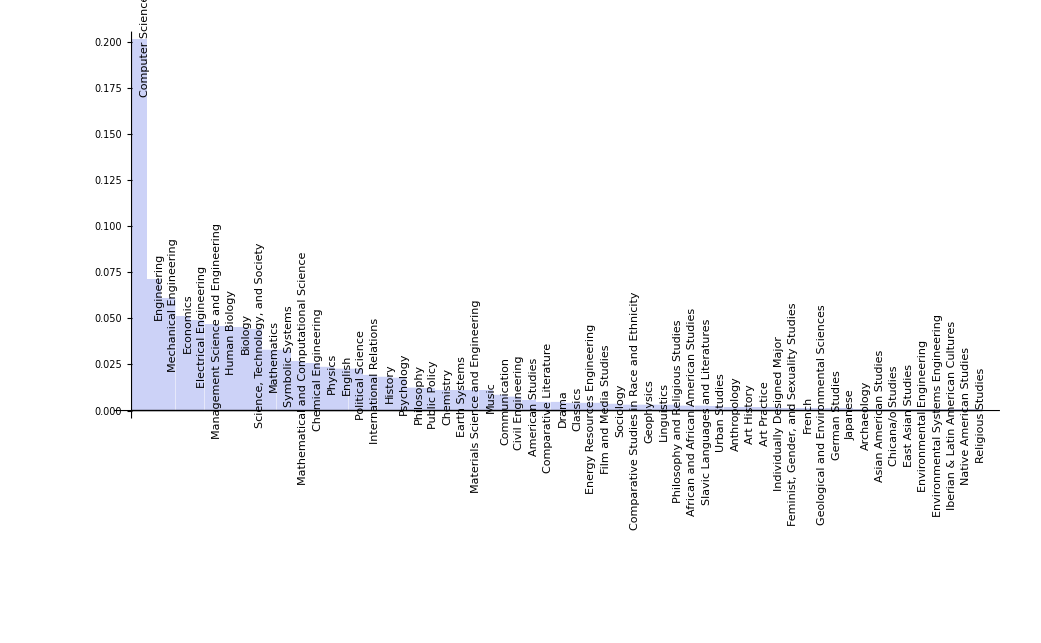

```mathematica
With[{col=2},BarChart[#[[;;,col]]/Total@#[[;;,col]],ChartLabels->Placed[#[[;;,1]] ,Top,Rotate[#,Pi/2]&]]&@Select[#,#[[col]] > 0&]&@SortBy[#,-#[[col]]&]]&@data15
```

```mathematica
Transpose[Transpose[#][[;;1]]~Join~MapThread[Divide,{Transpose[#][[2;;]],(Total/@Transpose[#][[2;;]])}]]&@data15
```

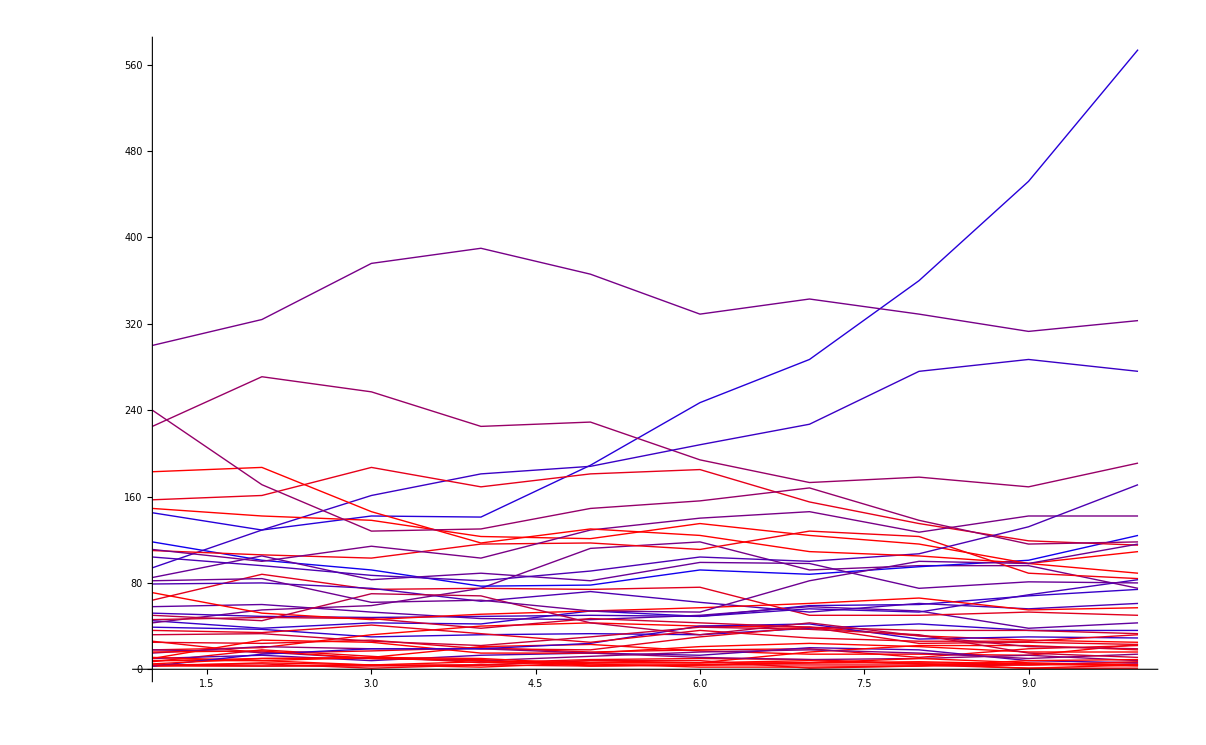

```mathematica
ListLinePlot[Transpose@{Range@Length@#,#}&/@#[[;;,2;;]],PlotRange->Full,AxesOrigin->{1,0},PlotStyle->({Thick,#}&/@(#[[;;,1]]/.techcolor))]&@Flatten[Cases[GatherBy[Join@@#,First],ConstantArray[_,Length@#]],{{1},{2,3}}][[;;,{1}~Join~Table[2i,{i,1,Length@#}]]]&@(Sort@Select[#[[;;,{1,4}]],#[[2]]>0&]&/@Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07,data06})
```

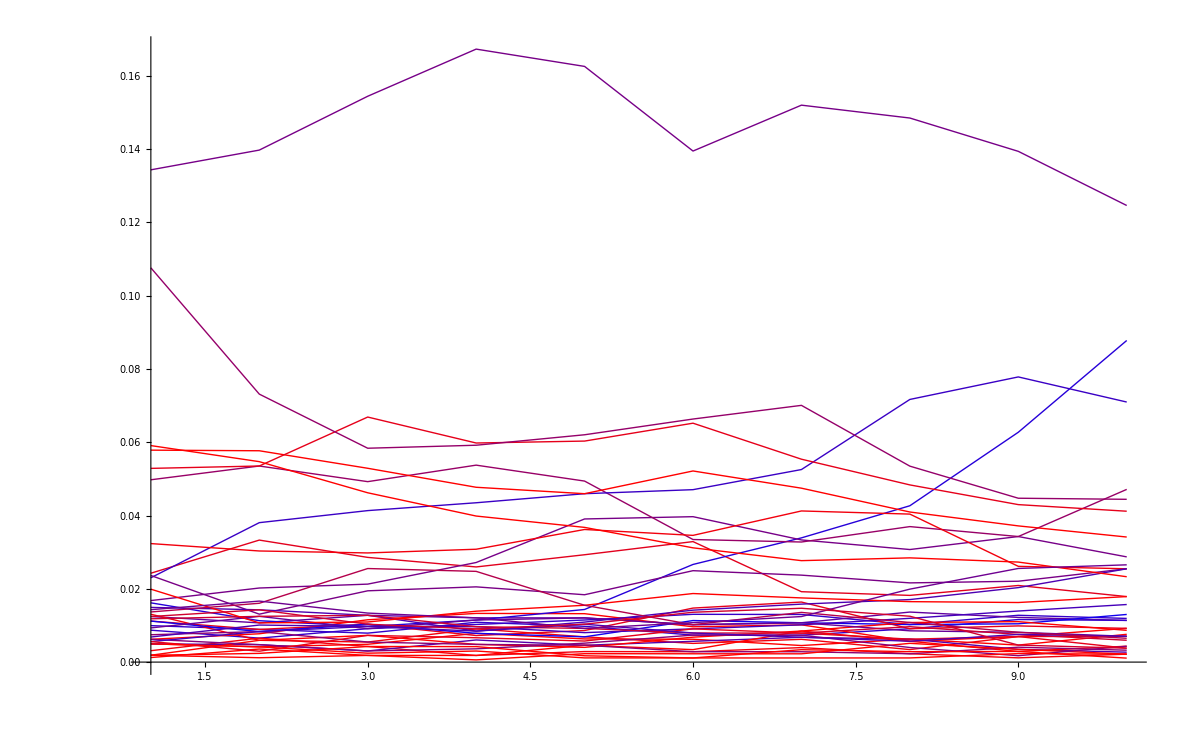

```mathematica
ListLinePlot[Transpose@{Range@Length@#,#}&/@#[[;;,2;;]],PlotRange->Full,AxesOrigin->{1,0},PlotStyle->({Thick,#}&/@(#[[;;,1]]/.techcolor))]&@Flatten[Cases[GatherBy[Join@@#,First],ConstantArray[_,Length@#]],{{1},{2,3}}][[;;,{1}~Join~Table[2i,{i,1,Length@#}]]]&@
(Sort@Select[#[[;;,{1,3}]],#[[2]]>0&]&/@(Transpose[Transpose[#][[;;1]]~Join~MapThread[Divide,{Transpose[#][[2;;]],(Total/@Transpose[#][[2;;]])}]]&/@
(Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07,data06})))
```

Problems: CS/engineering majors declare earlier (not dividing by total class size at graduation - this is just total declared undergrads)

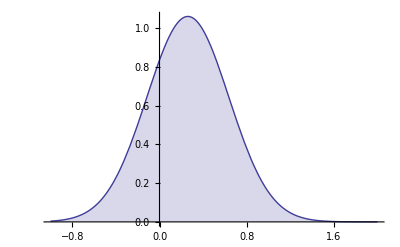

```mathematica
Plot[PDF[#,x]&@NormalDistribution[0.260164,(1.39-0.260164)/3],{x,-1,2},Filling->Axis]
```

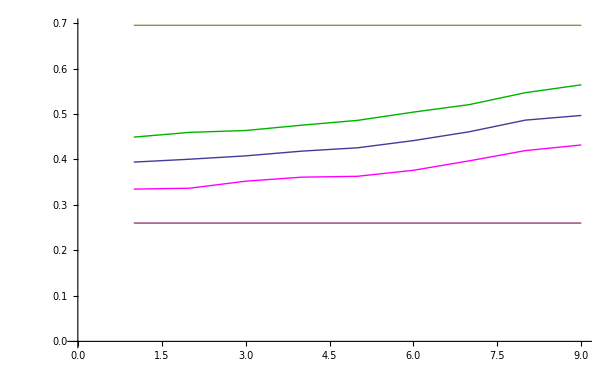

```mathematica
ListLinePlot[MapThread[List,{Range[9],#}]&/@
{Total[Times@@MapAt[Norm[#/.techtable]&,#,1]/2&/@#[[;;,{1,4}]]/Total@#[[;;,4]]]&@Select[#,#[[4]]>0&]&/@Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07},0.260164&/@Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07},
1.39/2&/@Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07},Total[Times@@MapAt[Norm[#/.techtable]&,#,1]/2&/@#[[;;,{1,3}]]/Total@#[[;;,3]]]&@Select[#,#[[4]]>0&]&/@Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07},Total[Times@@MapAt[Norm[#/.techtable]&,#,1]/2&/@#[[;;,{1,2}]]/Total@#[[;;,2]]]&@Select[#,#[[4]]>0&]&/@Reverse@{data15,data14,data13,data12,data11,data10,data09,data08,data07}
}
,AxesOrigin->{0,0},PlotStyle->{Automatic,Automatic,Automatic,RGBColor[1,0,1],RGBColor[0,0.7,0]}]
```

```mathematica
SortBy[#~Join~{Norm@#[[2;;]]}&/@techcoeff,-#[[-1]]&]//TableForm[#,TableHeadings->{{},{"Major","S","T","E","M","Norm"}}]&
```

| Major | S | T | E | M | Norm
 | Electrical Engineering | 0.7 | 1 | 1 | 1 | 1.86815
 | Computer Science | 0.3 | 1 | 1 | 0.9 | 1.70294
 | Civil Engineering | 0.5 | 0.8 | 1 | 0.8 | 1.5906
 | Chemical Engineering | 0.7 | 0.8 | 1 | 0.6 | 1.57797
 | Engineering | 0.5 | 0.8 | 1 | 0.7 | 1.54272
 | Materials Science and Engineering | 0.8 | 0.7 | 1 | 0.5 | 1.54272
 | Mathematical and Computational Science | 0 | 0.8 | 0.7 | 1 | 1.45945
 | Physics | 1 | 0.3 | 0.2 | 0.9 | 1.39284
 | Mechanical Engineering | 0.3 | 0.7 | 1 | 0.6 | 1.39284
 | Environmental Engineering | 0.7 | 0.4 | 1 | 0.3 | 1.31909
 | Environmental Systems Engineering | 0.7 | 0.4 | 1 | 0.3 | 1.31909
 | Chemistry | 1 | 0.4 | 0.2 | 0.6 | 1.249
 | Energy Resources Engineering | 0.3 | 0.5 | 1 | 0.4 | 1.22474
 | Mathematics | 0 | 0.6 | 0.2 | 1 | 1.18322
 | Petroleum Engineering | 0.3 | 0.5 | 1 | 0.2 | 1.17473
 | Symbolic Systems | 0.3 | 0.7 | 0.6 | 0.6 | 1.14018
 | Industrial Engineering | 0.2 | 0.3 | 1 | 0.4 | 1.13578
 | Earth Systems | 0.8 | 0.4 | 0.5 | 0.3 | 1.06771
 | Biological Sciences | 1 | 0.3 | 0 | 0.2 | 1.06301
 | Biology | 1 | 0.3 | 0 | 0.2 | 1.06301
 | Human Biology | 1 | 0.2 | 0 | 0.3 | 1.06301
 | Management Science and Engineering | 0.3 | 0.6 | 0.4 | 0.7 | 1.04881
 | Statistics | 0 | 0.3 | 0.1 | 1 | 1.04881
 | Linguistics | 0.4 | 0.6 | 0.2 | 0.6 | 0.959166
 | Geophysics | 0.9 | 0 | 0 | 0.3 | 0.948683
 | Geological and Environmental Sciences | 0.7 | 0.4 | 0.2 | 0.3 | 0.883176
 | Psychology | 0.8 | 0.2 | 0 | 0.1 | 0.830662
 | Economics | 0.4 | 0.3 | 0.2 | 0.6 | 0.806226
 | Science and Technology and Society | 0.4 | 0.4 | 0.2 | 0 | 0.6
 | Science, Technology, and Society | 0.4 | 0.4 | 0.2 | 0 | 0.6
 | Science Technology and Society | 0.4 | 0.4 | 0.2 | 0 | 0.6
 | Sociology | 0.5 | 0.1 | 0 | 0.3 | 0.591608
 | Archaeology | 0.2 | 0.3 | 0.2 | 0 | 0.412311
 | Anthropological Sciences | 0.4 | 0.1 | 0 | 0 | 0.412311
 | Anthropology | 0.4 | 0 | 0 | 0 | 0.4
 | Music | 0.3 | 0.2 | 0.1 | 0.1 | 0.387298
 | Urban Studies | 0.3 | 0 | 0 | 0.2 | 0.360555
 | Cultural and Social Anthropology | 0.3 | 0 | 0 | 0 | 0.3
 | Communication | 0.1 | 0.2 | 0 | 0 | 0.223607
 | Comparative Studies in Race and Ethnicity | 0.2 | 0 | 0 | 0 | 0.2
 | International Relations | 0.2 | 0 | 0 | 0 | 0.2
 | Philosophy | 0 | 0 | 0 | 0.2 | 0.2
 | African and African American Studies | 0.1 | 0 | 0 | 0 | 0.1
 | American Studies | 0.1 | 0 | 0 | 0 | 0.1
 | Art | 0 | 0.1 | 0 | 0 | 0.1
 | Asian American Studies | 0.1 | 0 | 0 | 0 | 0.1
 | Chicana and Chicano Studies | 0.1 | 0 | 0 | 0 | 0.1
 | Chicana/o Studies | 0.1 | 0 | 0 | 0 | 0.1
 | Drama | 0.1 | 0 | 0 | 0 | 0.1
 | East Asian Studies | 0.1 | 0 | 0 | 0 | 0.1
 | History | 0.1 | 0 | 0 | 0 | 0.1
 | Philosophy and Religious Studies | 0 | 0 | 0 | 0.1 | 0.1
 | Art History | 0 | 0 | 0 | 0 | 0
 | Art Practice | 0 | 0 | 0 | 0 | 0
 | Chinese | 0 | 0 | 0 | 0 | 0
 | Classics | 0 | 0 | 0 | 0 | 0
 | Comparative Literature | 0 | 0 | 0 | 0 | 0
 | English | 0 | 0 | 0 | 0 | 0
 | English and French Literature | 0 | 0 | 0 | 0 | 0
 | English and German Literatures | 0 | 0 | 0 | 0 | 0
 | English and Italian Literature | 0 | 0 | 0 | 0 | 0
 | English and Spanish Literature | 0 | 0 | 0 | 0 | 0
 | Feminist, Gender, and Sexuality Studies | 0 | 0 | 0 | 0 | 0
 | Feminist Studies | 0 | 0 | 0 | 0 | 0
 | Film and Media Studies | 0 | 0 | 0 | 0 | 0
 | French | 0 | 0 | 0 | 0 | 0
 | German Studies | 0 | 0 | 0 | 0 | 0
 | Humanities | 0 | 0 | 0 | 0 | 0
 | Iberian & Latin American Cultures | 0 | 0 | 0 | 0 | 0
 | Individually Designed Major | 0 | 0 | 0 | 0 | 0
 | International Policy Studies | 0 | 0 | 0 | 0 | 0
 | Italian | 0 | 0 | 0 | 0 | 0
 | Japanese | 0 | 0 | 0 | 0 | 0
 | Native American Studies | 0 | 0 | 0 | 0 | 0
 | Political Science | 0 | 0 | 0 | 0 | 0
 | Public Policy | 0 | 0 | 0 | 0 | 0
 | Religious Studies | 0 | 0 | 0 | 0 | 0
 | Slavic Languages and Literatures | 0 | 0 | 0 | 0 | 0
 | Spanish | 0 | 0 | 0 | 0 | 0

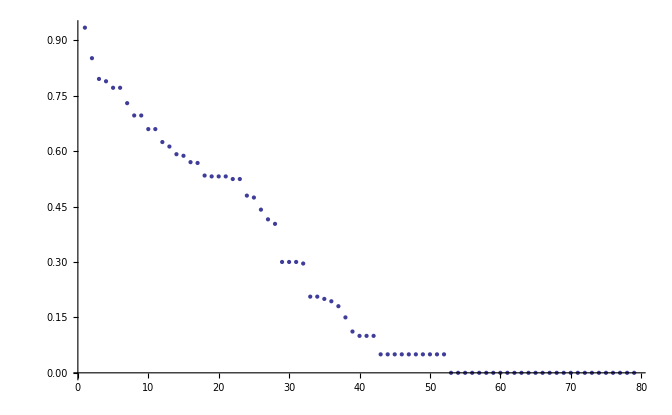

1326.84

```mathematica
SortBy[#~Join~{1/2Norm@#[[2;;]]}&/@techcoeff,-#[[-1]]&][[;;,6]]//ListPlot[#,PlotRange->Full,PlotStyle->PointSize->Large]&
0.260164*5100
```

```mathematica
1/2Norm@#[[2;;]]&/@techcoeff//{Mean@#,Median@#}&
```

{0.260038,0.1}

Agglomerate::ties: 30 ties have been detected; reordering input may produce a different result.

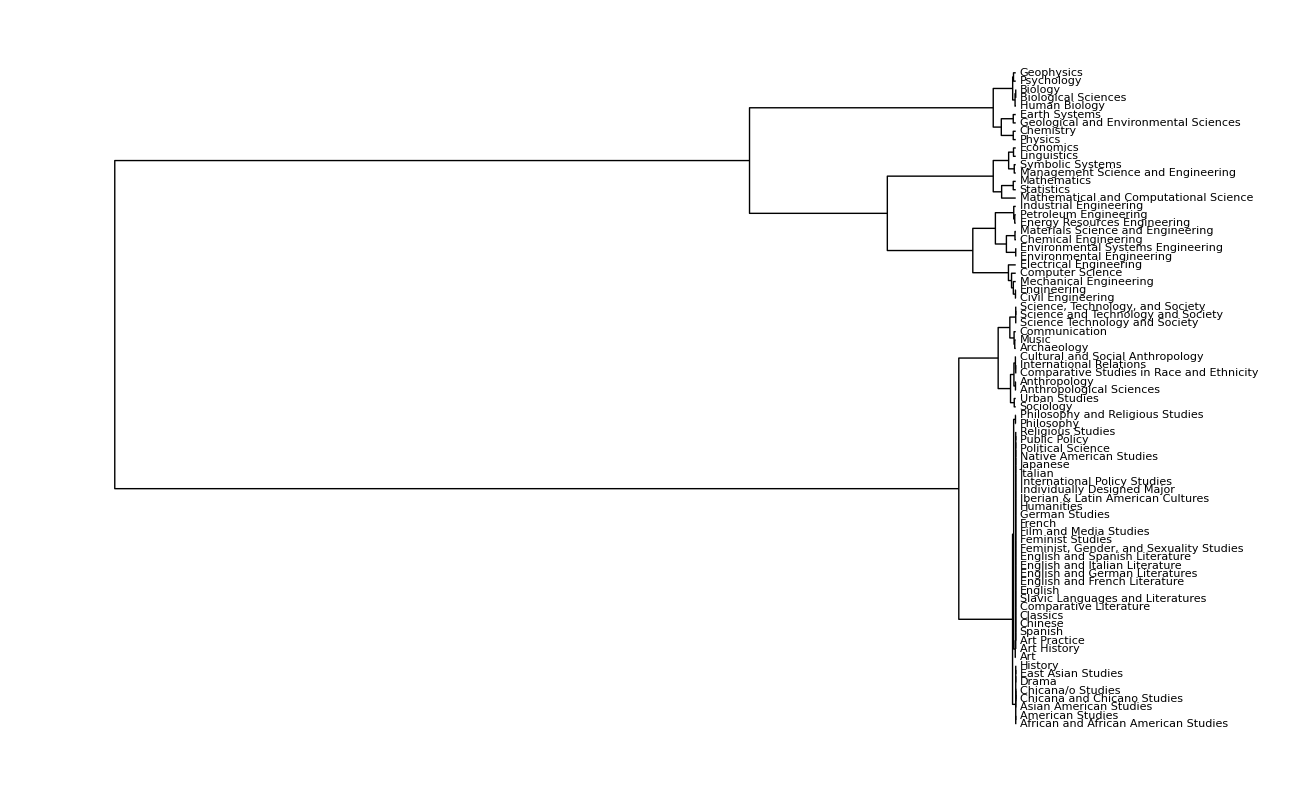

```mathematica
Needs["HierarchicalClustering`"]
DendrogramPlot[#,LeafLabels->(#&),Orientation->Left]&@Agglomerate[techcoeff[[;;,2;;]]->techcoeff[[;;,1]],Linkage->"Ward"]
```